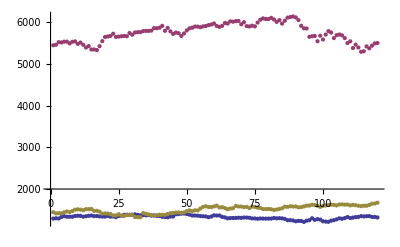

```mathematica
{hedge,dax,d2}=Transpose[Import["c:\\kurse.dat","Table"]];ListPlot[{hedge,dax,d2}]
```

```mathematica
hedge=Log[hedge];dax=Log[dax];d2=Log[d2];
```

```mathematica
hedge=Differences[hedge];
```

```mathematica
dax=Differences[dax];d2=Differences[d2];
```

```mathematica
w=Transpose[{hedge,dax,d2}];
```

```mathematica
w=Sort[w,#1[[1]]<#2[[1]]&];
```

```mathematica
hedge=Transpose[w][[1]];
dax=Transpose[w][[2]];
d2=Transpose[w][[3]];
```

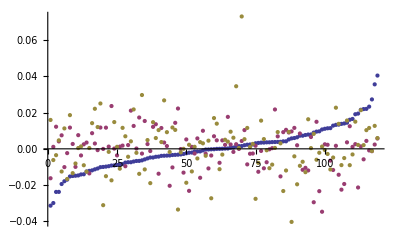

```mathematica
ListPlot[Transpose[w][[1;;3]],PlotRange->All]
```

```mathematica
min0=Min[Transpose[w][[1]]];wN=Length[hedge];nn=wN;
max0=Max[Transpose[w][[1]]];
min1=Min[Transpose[w][[2]]];
max1=Max[Transpose[w][[2]]];
```

```mathematica
U={};sdax=Sort[dax];AppendTo[U,{max0,max1,1}];

For[i=1,i≤nn,i++,
AppendTo[U,{hedge[[i]],max1,(i-1)/nn}];
AppendTo[U,{max0,sdax[[i]],(i-1)/nn}];
AppendTo[U,{hedge[[i]],min1,0}];
AppendTo[U,{min0,sdax[[i]],0}];
]
```

```mathematica
F={};For[i=1,i≤wN,i++,
AppendTo[F,{w[[i,1]],w[[i,2]],Length[Select[w,#[[1]]<=w[[i,1]]  && #[[2]]<=w[[i,2]]&]]/wN}];
]
```

```mathematica
W=Join[F,U];
```

```mathematica
ListPointPlot3D[W]
```

-Graphics3D-

```mathematica
hedgeI=Table[{hedge[[i]],(i-1)/(nn-1)},{i,nn}];
daxI=Table[{sdax[[i]],(i-1)/(nn-1)},{i,nn}];W=F;Co=Table[{Select[hedgeI,#[[1]]==W[[i,1]]&][[1,2]],Select[daxI,#[[1]]==W[[i,2]]&][[1,2]],W[[i,3]]},{i,Length[W]}];AppendTo[Co,{1,0,0}];AppendTo[Co,{0,1,0}];AppendTo[Co,{0,0,0}];AppendTo[Co,{1,1,1}];
```

```mathematica
ListPointPlot3D[Co]
```

-Graphics3D-

```mathematica
h=Import["C:\\delaunay.txt","Table"]
g=Import["c:\\copulasample.txt","Table"];cc=Drop[Import["c:\\empcopula.dat","Table"],1];c=Transpose[{#[[1]],#[[2]],#[[4]]}&[Transpose[cc]]];cc=Transpose[Transpose[cc][[1;;3]]];hh=Table[Subsets[h[[i]],{3}],{i,Length[h]}][[3]];
Graphics3D[{{PointSize[Large],Red,Table[Point[c[[i]]],{i,Length[c]}]},{PointSize[Large],Blue,Point[c[[8]]]},{Opacity[0.1],Table[Polygon[c[[#+1]]&/@hh[[j]]],{j,Length[hh]}]}}]
```

{{0,7,8,12},{0,7,8,13},{0,7,12,22},{0,7,13,22},{0,8,10,13},{0,8,10,14},{0,8,12,14},{0,10,13,21},{0,10,14,21},{0,12,14,16},{0,12,16,22},{0,13,17,21},{0,13,17,22},{0,14,16,21},{0,16,17,21},{0,16,17,22},{0,16,21,22},{0,17,21,22},{1,3,4,5},{1,3,4,6},{1,3,5,7},{1,3,6,8},{1,3,7,8},{1,4,5,22},{1,4,6,18},{1,4,18,22},{1,5,7,22},{1,6,8,9},{1,6,9,15},{1,6,15,18},{1,7,8,13},{1,7,9,13},{1,8,9,13},{2,3,4,6},{2,3,4,11},{2,3,6,8},{2,3,8,11},{2,4,6,11},{2,6,8,9},{2,6,9,15},{2,6,11,19},{2,6,15,19},{2,8,9,13},{2,8,10,13},{2,8,10,14},{2,8,11,14},{2,9,13,19},{2,9,15,19},{2,10,13,19},{2,10,14,19},{2,11,14,19},{3,4,5,11},{3,5,7,12},{3,5,8,12},{3,5,8,14},{3,5,11,14},{3,7,8,12},{3,8,11,14},{4,5,11,18},{4,5,18,22},{4,6,11,18},{5,7,12,22},{5,8,12,14},{5,11,14,20},{5,11,18,20},{5,12,14,16},{5,12,16,22},{5,14,16,20},{6,11,15,18},{6,11,15,19},{7,9,13,17},{7,13,17,22},{9,10,13,15},{9,10,13,19},{9,10,15,19},{9,13,15,17},{10,13,15,17},{10,13,17,21},{10,14,16,20},{10,14,16,21},{10,14,19,20},{10,16,19,20},{10,16,19,21},{10,16,20,21},{10,19,20,21},{11,14,19,20}}

-Graphics3D-

```mathematica
f[B[[1]]]/ccc//N
```

0.723532

```mathematica
S=h[[3]]
```

{0,7,12,22}

```mathematica
B={{1,2,3,4}};
```

```mathematica
For[i=1,i≤3,i++,AppendTo[B,RotateLeft[B[[Length[B]]]]]]
```

```mathematica
B
```

{{1,2,3,4},{2,3,4,1},{3,4,1,2},{4,1,2,3}}

```mathematica
RotateLeft[%]
```

{3,4,1,2}

```mathematica
S[[#]]&/@%
```

{7,12,22,0}

```mathematica
f[u_]:=Abs[2*ArcTan[t[{#[[1]],#[[2]],#[[3]]}-{1,1,1}#[[4]]&[c[[#+1]]&/@(S[[#]]&/@u)]]]]/Pi//N
```

```mathematica
ccc=f[B[[1]]]+f[B[[2]]]+f[B[[3]]]+f[B[[4]]]
```

0.524036

```mathematica
4/3//N
```

1.33333

```mathematica
t=.
```

```mathematica
t[R_]:=Det[R]/(Norm[R[[1]]]Norm[R[[2]]]Norm[R[[3]]]+(R[[1]].R[[2]])*Norm[R[[3]]]+(R[[2]].R[[3]])*Norm[R[[1]]]+(R[[3]].R[[1]])*Norm[R[[2]]])
```

```mathematica
c[[1]]
```

{10,7,8}

```mathematica
ce=c[[3;;7]];
```

```mathematica
ce={{0.23564142713114022,0.19380998628864599,0.594495511815069},{0.6525572153791819,0.24694329925782044,0.7672917678839029},{0.9163123444125463,0.026621532304647255,0.3715576391209683},{0.2668950744537262,0.7975001767040044,0.7934023887167383},{0.7641225411392012,0.2966207983489944,0.1456840182999719}}
```

{{0.235641,0.19381,0.594496},{0.652557,0.246943,0.767292},{0.916312,0.0266215,0.371558},{0.266895,0.7975,0.793402},{0.764123,0.296621,0.145684}}

```mathematica
{{0.23564142713114022,0.19380998628864599,0.594495511815069},{0.6525572153791819,0.24694329925782044,0.7672917678839029},{0.3163123444125463,0.026621532304647255,0.3715576391209683},{0.2668950744537262,0.7975001767040044,0.7934023887167383},{0.7641225411392012,0.8966207983489944,0.1456840182999719}}
```

```mathematica
ListPointPlot3D[{ce,  {a}},PlotStyle->PointSize[Large]]
```

-Graphics3D-

```mathematica
a={1,2,3};
```

```mathematica
Det[
```

```mathematica
Export["c:\\empCopula.dat",RandomReal[1,{7,4}]]
```

c:\empCopula.dat

-Graphics3D-

```mathematica
ListPointPlot3D[cc,PlotStyle->PointSize[Large]]
```

-Graphics3D-

```mathematica
Show[ListPointPlot3D[{#[[1]],#[[2]],#[[3]]+0.01}&/@c,PlotStyle->Red],ListPointPlot3D[Co]]
```

-Graphics3D-

```mathematica
Show[ListPlot3D[c,Mesh->All],ListPointPlot3D[c,PlotStyle->Red],AspectRatio->1]
```

-Graphics3D-

```mathematica
y=.
```

```mathematica
Plot3D[Interpolation[c][x,y],{x,0,1},{y,0,1}]
```

Interpolation::indim: The coordinates do not lie on a structured tensor product grid.

General::stop: Further output of Interpolation :: "indim" will be suppressed during this calculation.

-Graphics3D-

```mathematica
Graphics3D[{{PointSize[Large],Red,Table[Point[c[[i]]],{i,Length[c]}]},{Table[Polygon[c[[#+1]]&/@h[[j]]],{j,Length[h]}]}}]
```

-Graphics3D-

```mathematica
ListPointPlot3D[{g}]
```

-Graphics3D-

```mathematica
Show[ListPointPlot3D[c,PlotStyle->Red],ListPlot3D[g,InterpolationOrder->1,Mesh->{20,20}],AspectRatio->1]
```

-Graphics3D-

```mathematica
f[i_]:={C[i][0],C[i][1],C[i][2],C[i][0]^2+C[i][1]^2+C[i][2]^2};Det[{f[h],f[i],f[j],f[k]}]
```

C[h][2] C[i][1] (C[j][0])^2 C[k][0]-C[h][1] C[i][2] (C[j][0])^2 C[k][0]-C[h][2] (C[i][0])^2 C[j][1] C[k][0]-C[h][2] (C[i][1])^2 C[j][1] C[k][0]+(C[h][0])^2 C[i][2] C[j][1] C[k][0]+(C[h][1])^2 C[i][2] C[j][1] C[k][0]+(C[h][2])^2 C[i][2] C[j][1] C[k][0]-C[h][2] (C[i][2])^2 C[j][1] C[k][0]+C[h][2] C[i][1] (C[j][1])^2 C[k][0]-C[h][1] C[i][2] (C[j][1])^2 C[k][0]+C[h][1] (C[i][0])^2 C[j][2] C[k][0]-(C[h][0])^2 C[i][1] C[j][2] C[k][0]-(C[h][1])^2 C[i][1] C[j][2] C[k][0]-(C[h][2])^2 C[i][1] C[j][2] C[k][0]+C[h][1] (C[i][1])^2 C[j][2] C[k][0]+C[h][1] (C[i][2])^2 C[j][2] C[k][0]+C[h][2] C[i][1] (C[j][2])^2 C[k][0]-C[h][1] C[i][2] (C[j][2])^2 C[k][0]-C[h][2] C[i][1] C[j][0] (C[k][0])^2+C[h][1] C[i][2] C[j][0] (C[k][0])^2+C[h][2] C[i][0] C[j][1] (C[k][0])^2-C[h][0] C[i][2] C[j][1] (C[k][0])^2-C[h][1] C[i][0] C[j][2] (C[k][0])^2+C[h][0] C[i][1] C[j][2] (C[k][0])^2+C[h][2] (C[i][0])^2 C[j][0] C[k][1]+C[h][2] (C[i][1])^2 C[j][0] C[k][1]-(C[h][0])^2 C[i][2] C[j][0] C[k][1]-(C[h][1])^2 C[i][2] C[j][0] C[k][1]-(C[h][2])^2 C[i][2] C[j][0] C[k][1]+C[h][2] (C[i][2])^2 C[j][0] C[k][1]-C[h][2] C[i][0] (C[j][0])^2 C[k][1]+C[h][0] C[i][2] (C[j][0])^2 C[k][1]-C[h][2] C[i][0] (C[j][1])^2 C[k][1]+C[h][0] C[i][2] (C[j][1])^2 C[k][1]+(C[h][0])^2 C[i][0] C[j][2] C[k][1]+(C[h][1])^2 C[i][0] C[j][2] C[k][1]+(C[h][2])^2 C[i][0] C[j][2] C[k][1]-C[h][0] (C[i][0])^2 C[j][2] C[k][1]-C[h][0] (C[i][1])^2 C[j][2] C[k][1]-C[h][0] (C[i][2])^2 C[j][2] C[k][1]-C[h][2] C[i][0] (C[j][2])^2 C[k][1]+C[h][0] C[i][2] (C[j][2])^2 C[k][1]-C[h][2] C[i][1] C[j][0] (C[k][1])^2+C[h][1] C[i][2] C[j][0] (C[k][1])^2+C[h][2] C[i][0] C[j][1] (C[k][1])^2-C[h][0] C[i][2] C[j][1] (C[k][1])^2-C[h][1] C[i][0] C[j][2] (C[k][1])^2+C[h][0] C[i][1] C[j][2] (C[k][1])^2-C[h][1] (C[i][0])^2 C[j][0] C[k][2]+(C[h][0])^2 C[i][1] C[j][0] C[k][2]+(C[h][1])^2 C[i][1] C[j][0] C[k][2]+(C[h][2])^2 C[i][1] C[j][0] C[k][2]-C[h][1] (C[i][1])^2 C[j][0] C[k][2]-C[h][1] (C[i][2])^2 C[j][0] C[k][2]+C[h][1] C[i][0] (C[j][0])^2 C[k][2]-C[h][0] C[i][1] (C[j][0])^2 C[k][2]-(C[h][0])^2 C[i][0] C[j][1] C[k][2]-(C[h][1])^2 C[i][0] C[j][1] C[k][2]-(C[h][2])^2 C[i][0] C[j][1] C[k][2]+C[h][0] (C[i][0])^2 C[j][1] C[k][2]+C[h][0] (C[i][1])^2 C[j][1] C[k][2]+C[h][0] (C[i][2])^2 C[j][1] C[k][2]+C[h][1] C[i][0] (C[j][1])^2 C[k][2]-C[h][0] C[i][1] (C[j][1])^2 C[k][2]+C[h][1] C[i][0] (C[j][2])^2 C[k][2]-C[h][0] C[i][1] (C[j][2])^2 C[k][2]-C[h][2] C[i][1] C[j][0] (C[k][2])^2+C[h][1] C[i][2] C[j][0] (C[k][2])^2+C[h][2] C[i][0] C[j][1] (C[k][2])^2-C[h][0] C[i][2] C[j][1] (C[k][2])^2-C[h][1] C[i][0] C[j][2] (C[k][2])^2+C[h][0] C[i][1] C[j][2] (C[k][2])^2

```mathematica
CForm[Expand[%]]
```

C(h)(2)*C(i)(1)*Power(C(j)(0),2)*C(k)(0) - C(h)(1)*C(i)(2)*Power(C(j)(0),2)*C(k)(0) - C(h)(2)*Power(C(i)(0),2)*C(j)(1)*C(k)(0) - 
   C(h)(2)*Power(C(i)(1),2)*C(j)(1)*C(k)(0) + Power(C(h)(0),2)*C(i)(2)*C(j)(1)*C(k)(0) + 
   Power(C(h)(1),2)*C(i)(2)*C(j)(1)*C(k)(0) + Power(C(h)(2),2)*C(i)(2)*C(j)(1)*C(k)(0) - 
   C(h)(2)*Power(C(i)(2),2)*C(j)(1)*C(k)(0) + C(h)(2)*C(i)(1)*Power(C(j)(1),2)*C(k)(0) - 
   C(h)(1)*C(i)(2)*Power(C(j)(1),2)*C(k)(0) + C(h)(1)*Power(C(i)(0),2)*C(j)(2)*C(k)(0) - 
   Power(C(h)(0),2)*C(i)(1)*C(j)(2)*C(k)(0) - Power(C(h)(1),2)*C(i)(1)*C(j)(2)*C(k)(0) - 
   Power(C(h)(2),2)*C(i)(1)*C(j)(2)*C(k)(0) + C(h)(1)*Power(C(i)(1),2)*C(j)(2)*C(k)(0) + 
   C(h)(1)*Power(C(i)(2),2)*C(j)(2)*C(k)(0) + C(h)(2)*C(i)(1)*Power(C(j)(2),2)*C(k)(0) - 
   C(h)(1)*C(i)(2)*Power(C(j)(2),2)*C(k)(0) - C(h)(2)*C(i)(1)*C(j)(0)*Power(C(k)(0),2) + 
   C(h)(1)*C(i)(2)*C(j)(0)*Power(C(k)(0),2) + C(h)(2)*C(i)(0)*C(j)(1)*Power(C(k)(0),2) - 
   C(h)(0)*C(i)(2)*C(j)(1)*Power(C(k)(0),2) - C(h)(1)*C(i)(0)*C(j)(2)*Power(C(k)(0),2) + 
   C(h)(0)*C(i)(1)*C(j)(2)*Power(C(k)(0),2) + C(h)(2)*Power(C(i)(0),2)*C(j)(0)*C(k)(1) + 
   C(h)(2)*Power(C(i)(1),2)*C(j)(0)*C(k)(1) - Power(C(h)(0),2)*C(i)(2)*C(j)(0)*C(k)(1) - 
   Power(C(h)(1),2)*C(i)(2)*C(j)(0)*C(k)(1) - Power(C(h)(2),2)*C(i)(2)*C(j)(0)*C(k)(1) + 
   C(h)(2)*Power(C(i)(2),2)*C(j)(0)*C(k)(1) - C(h)(2)*C(i)(0)*Power(C(j)(0),2)*C(k)(1) + 
   C(h)(0)*C(i)(2)*Power(C(j)(0),2)*C(k)(1) - C(h)(2)*C(i)(0)*Power(C(j)(1),2)*C(k)(1) + 
   C(h)(0)*C(i)(2)*Power(C(j)(1),2)*C(k)(1) + Power(C(h)(0),2)*C(i)(0)*C(j)(2)*C(k)(1) + 
   Power(C(h)(1),2)*C(i)(0)*C(j)(2)*C(k)(1) + Power(C(h)(2),2)*C(i)(0)*C(j)(2)*C(k)(1) - 
   C(h)(0)*Power(C(i)(0),2)*C(j)(2)*C(k)(1) - C(h)(0)*Power(C(i)(1),2)*C(j)(2)*C(k)(1) - 
   C(h)(0)*Power(C(i)(2),2)*C(j)(2)*C(k)(1) - C(h)(2)*C(i)(0)*Power(C(j)(2),2)*C(k)(1) + 
   C(h)(0)*C(i)(2)*Power(C(j)(2),2)*C(k)(1) - C(h)(2)*C(i)(1)*C(j)(0)*Power(C(k)(1),2) + 
   C(h)(1)*C(i)(2)*C(j)(0)*Power(C(k)(1),2) + C(h)(2)*C(i)(0)*C(j)(1)*Power(C(k)(1),2) - 
   C(h)(0)*C(i)(2)*C(j)(1)*Power(C(k)(1),2) - C(h)(1)*C(i)(0)*C(j)(2)*Power(C(k)(1),2) + 
   C(h)(0)*C(i)(1)*C(j)(2)*Power(C(k)(1),2) - C(h)(1)*Power(C(i)(0),2)*C(j)(0)*C(k)(2) + 
   Power(C(h)(0),2)*C(i)(1)*C(j)(0)*C(k)(2) + Power(C(h)(1),2)*C(i)(1)*C(j)(0)*C(k)(2) + 
   Power(C(h)(2),2)*C(i)(1)*C(j)(0)*C(k)(2) - C(h)(1)*Power(C(i)(1),2)*C(j)(0)*C(k)(2) - 
   C(h)(1)*Power(C(i)(2),2)*C(j)(0)*C(k)(2) + C(h)(1)*C(i)(0)*Power(C(j)(0),2)*C(k)(2) - 
   C(h)(0)*C(i)(1)*Power(C(j)(0),2)*C(k)(2) - Power(C(h)(0),2)*C(i)(0)*C(j)(1)*C(k)(2) - 
   Power(C(h)(1),2)*C(i)(0)*C(j)(1)*C(k)(2) - Power(C(h)(2),2)*C(i)(0)*C(j)(1)*C(k)(2) + 
   C(h)(0)*Power(C(i)(0),2)*C(j)(1)*C(k)(2) + C(h)(0)*Power(C(i)(1),2)*C(j)(1)*C(k)(2) + 
   C(h)(0)*Power(C(i)(2),2)*C(j)(1)*C(k)(2) + C(h)(1)*C(i)(0)*Power(C(j)(1),2)*C(k)(2) - 
   C(h)(0)*C(i)(1)*Power(C(j)(1),2)*C(k)(2) + C(h)(1)*C(i)(0)*Power(C(j)(2),2)*C(k)(2) - 
   C(h)(0)*C(i)(1)*Power(C(j)(2),2)*C(k)(2) - C(h)(2)*C(i)(1)*C(j)(0)*Power(C(k)(2),2) + 
   C(h)(1)*C(i)(2)*C(j)(0)*Power(C(k)(2),2) + C(h)(2)*C(i)(0)*C(j)(1)*Power(C(k)(2),2) - 
   C(h)(0)*C(i)(2)*C(j)(1)*Power(C(k)(2),2) - C(h)(1)*C(i)(0)*C(j)(2)*Power(C(k)(2),2) + C(h)(0)*C(i)(1)*C(j)(2)*Power(C(k)(2),2)

```mathematica
f[k]
```

{C[k][0],C[k][1],C[k][2],C[i][0]*C[i][0]+C[i][1]*C[i][1]+C[i][2]*C[i][2],1}

```mathematica
Expand[Det[{f[h],f[i],f[j],f[k]}]]
```

-C[h][2] C[i][1] C[j][0]+C[h][1] C[i][2] C[j][0]+C[h][2] C[i][0] C[j][1]-C[h][0] C[i][2] C[j][1]-C[h][1] C[i][0] C[j][2]+C[h][0] C[i][1] C[j][2]+C[h][2] C[i][1] C[k][0]-C[h][1] C[i][2] C[k][0]-C[h][2] C[j][1] C[k][0]+C[i][2] C[j][1] C[k][0]+C[h][1] C[j][2] C[k][0]-C[i][1] C[j][2] C[k][0]-C[h][2] C[i][0] C[k][1]+C[h][0] C[i][2] C[k][1]+C[h][2] C[j][0] C[k][1]-C[i][2] C[j][0] C[k][1]-C[h][0] C[j][2] C[k][1]+C[i][0] C[j][2] C[k][1]+C[h][1] C[i][0] C[k][2]-C[h][0] C[i][1] C[k][2]-C[h][1] C[j][0] C[k][2]+C[i][1] C[j][0] C[k][2]+C[h][0] C[j][1] C[k][2]-C[i][0] C[j][1] C[k][2]

```mathematica
f[i_]:={C[i][0],C[i][1],C[i][2]};CForm[Expand[Det[{f[h],f[i],f[j]}]]]
```

-(C(h)(2)*C(i)(1)*C(j)(0)) + C(h)(1)*C(i)(2)*C(j)(0) + C(h)(2)*C(i)(0)*C(j)(1) - C(h)(0)*C(i)(2)*C(j)(1) - 
   C(h)(1)*C(i)(0)*C(j)(2) + C(h)(0)*C(i)(1)*C(j)(2)

```mathematica
a=Expand[Det[{f[h],f[i],f[j]}]]
```

-C[h][2] C[i][1] C[j][0]+C[h][1] C[i][2] C[j][0]+C[h][2] C[i][0] C[j][1]-C[h][0] C[i][2] C[j][1]-C[h][1] C[i][0] C[j][2]+C[h][0] C[i][1] C[j][2]+C[h][2] C[i][1] C[k][0]-C[h][1] C[i][2] C[k][0]-C[h][2] C[j][1] C[k][0]+C[i][2] C[j][1] C[k][0]+C[h][1] C[j][2] C[k][0]-C[i][1] C[j][2] C[k][0]-C[h][2] C[i][0] C[k][1]+C[h][0] C[i][2] C[k][1]+C[h][2] C[j][0] C[k][1]-C[i][2] C[j][0] C[k][1]-C[h][0] C[j][2] C[k][1]+C[i][0] C[j][2] C[k][1]+C[h][1] C[i][0] C[k][2]-C[h][0] C[i][1] C[k][2]-C[h][1] C[j][0] C[k][2]+C[i][1] C[j][0] C[k][2]+C[h][0] C[j][1] C[k][2]-C[i][0] C[j][1] C[k][2]

```mathematica
CForm[a]
```

-(C(h)(2)*C(i)(1)*C(j)(0)) + C(h)(1)*C(i)(2)*C(j)(0) + C(h)(2)*C(i)(0)*C(j)(1) - C(h)(0)*C(i)(2)*C(j)(1) - 
   C(h)(1)*C(i)(0)*C(j)(2) + C(h)(0)*C(i)(1)*C(j)(2) + C(h)(2)*C(i)(1)*C(k)(0) - C(h)(1)*C(i)(2)*C(k)(0) - 
   C(h)(2)*C(j)(1)*C(k)(0) + C(i)(2)*C(j)(1)*C(k)(0) + C(h)(1)*C(j)(2)*C(k)(0) - C(i)(1)*C(j)(2)*C(k)(0) - 
   C(h)(2)*C(i)(0)*C(k)(1) + C(h)(0)*C(i)(2)*C(k)(1) + C(h)(2)*C(j)(0)*C(k)(1) - C(i)(2)*C(j)(0)*C(k)(1) - 
   C(h)(0)*C(j)(2)*C(k)(1) + C(i)(0)*C(j)(2)*C(k)(1) + C(h)(1)*C(i)(0)*C(k)(2) - C(h)(0)*C(i)(1)*C(k)(2) - 
   C(h)(1)*C(j)(0)*C(k)(2) + C(i)(1)*C(j)(0)*C(k)(2) + C(h)(0)*C(j)(1)*C(k)(2) - C(i)(0)*C(j)(1)*C(k)(2)

```mathematica
b=Expand[Det[{f[h],f[i],f[j],f[k]}]]
```

-C[h][2] C[i][1] C[j][0]+C[h][1] C[i][2] C[j][0]+C[h][2] C[i][0] C[j][1]-C[h][0] C[i][2] C[j][1]-C[h][1] C[i][0] C[j][2]+C[h][0] C[i][1] C[j][2]+C[h][2] C[i][1] C[k][0]-C[h][1] C[i][2] C[k][0]-C[h][2] C[j][1] C[k][0]+C[i][2] C[j][1] C[k][0]+C[h][1] C[j][2] C[k][0]-C[i][1] C[j][2] C[k][0]-C[h][2] C[i][0] C[k][1]+C[h][0] C[i][2] C[k][1]+C[h][2] C[j][0] C[k][1]-C[i][2] C[j][0] C[k][1]-C[h][0] C[j][2] C[k][1]+C[i][0] C[j][2] C[k][1]+C[h][1] C[i][0] C[k][2]-C[h][0] C[i][1] C[k][2]-C[h][1] C[j][0] C[k][2]+C[i][1] C[j][0] C[k][2]+C[h][0] C[j][1] C[k][2]-C[i][0] C[j][1] C[k][2]

```mathematica
a-b
```

0

```mathematica
Needs["VectorAnalysis`"]
```

```mathematica
v[k_]:={C[k][0],C[k][1],C[k][2]};
```

```mathematica
n=CrossProduct[v[k]-v[i],v[j]-v[i]];Solve[({A[0],A[1],z}-v[i]).n==0,z][[1,1,2]]
```

(A[1] C[i][2] C[j][0]-A[0] C[i][2] C[j][1]-A[1] C[i][0] C[j][2]+A[0] C[i][1] C[j][2]-A[1] C[i][2] C[k][0]+C[i][2] C[j][1] C[k][0]+A[1] C[j][2] C[k][0]-C[i][1] C[j][2] C[k][0]+A[0] C[i][2] C[k][1]-C[i][2] C[j][0] C[k][1]-A[0] C[j][2] C[k][1]+C[i][0] C[j][2] C[k][1]+A[1] C[i][0] C[k][2]-A[0] C[i][1] C[k][2]-A[1] C[j][0] C[k][2]+C[i][1] C[j][0] C[k][2]+A[0] C[j][1] C[k][2]-C[i][0] C[j][1] C[k][2])/(C[i][1] C[j][0]-C[i][0] C[j][1]-C[i][1] C[k][0]+C[j][1] C[k][0]+C[i][0] C[k][1]-C[j][0] C[k][1])

```mathematica
D[%,A[0]]
```

(-C[i][2] C[j][1]+C[i][1] C[j][2]+C[i][2] C[k][1]-C[j][2] C[k][1]-C[i][1] C[k][2]+C[j][1] C[k][2])/(C[i][1] C[j][0]-C[i][0] C[j][1]-C[i][1] C[k][0]+C[j][1] C[k][0]+C[i][0] C[k][1]-C[j][0] C[k][1])

```mathematica
CForm[(A[1] C[i][2] C[j][0]-A[0] C[i][2] C[j][1]-A[1] C[i][0] C[j][2]+A[0] C[i][1] C[j][2]-A[1] C[i][2] C[k][0]+C[i][2] C[j][1] C[k][0]+A[1] C[j][2] C[k][0]-C[i][1] C[j][2] C[k][0]+A[0] C[i][2] C[k][1]-C[i][2] C[j][0] C[k][1]-A[0] C[j][2] C[k][1]+C[i][0] C[j][2] C[k][1]+A[1] C[i][0] C[k][2]-A[0] C[i][1] C[k][2]-A[1] C[j][0] C[k][2]+C[i][1] C[j][0] C[k][2]+A[0] C[j][1] C[k][2]-C[i][0] C[j][1] C[k][2])/(C[i][1] C[j][0]-C[i][0] C[j][1]-C[i][1] C[k][0]+C[j][1] C[k][0]+C[i][0] C[k][1]-C[j][0] C[k][1])]
```

(A(1)*C(i)(2)*C(j)(0) - A(0)*C(i)(2)*C(j)(1) - A(1)*C(i)(0)*C(j)(2) + A(0)*C(i)(1)*C(j)(2) - A(1)*C(i)(2)*C(k)(0) + C(i)(2)*C(j)(1)*C(k)(0) + A(1)*C(j)(2)*C(k)(0) - 
     C(i)(1)*C(j)(2)*C(k)(0) + A(0)*C(i)(2)*C(k)(1) - C(i)(2)*C(j)(0)*C(k)(1) - A(0)*C(j)(2)*C(k)(1) + C(i)(0)*C(j)(2)*C(k)(1) + A(1)*C(i)(0)*C(k)(2) - 
     A(0)*C(i)(1)*C(k)(2) - A(1)*C(j)(0)*C(k)(2) + C(i)(1)*C(j)(0)*C(k)(2) + A(0)*C(j)(1)*C(k)(2) - C(i)(0)*C(j)(1)*C(k)(2))/
   (C(i)(1)*C(j)(0) - C(i)(0)*C(j)(1) - C(i)(1)*C(k)(0) + C(j)(1)*C(k)(0) + C(i)(0)*C(k)(1) - C(j)(0)*C(k)(1))

```mathematica
Det[{{C[i][1],C[i][2],"C[i][1]*C[i][1]"+"C[i][2]*C[i][2]",1},{C[j][1],C[j][2],"C[j][1]*C[j][1]"+"C[j][2]*C[j][2]",1},{C[k][1],C[k][2],"C[k][1]*C[k][1]"+"C[k][2]*C[k][2]",1},{C[p][1],C[p][2],"C[p][1]*C[p][1]"+"C[p][2]*C[p][2]",1}}]
```

-C[k][1]*C[k][1] C[i][2] C[j][1]-C[k][2]*C[k][2] C[i][2] C[j][1]+C[p][1]*C[p][1] C[i][2] C[j][1]+C[p][2]*C[p][2] C[i][2] C[j][1]+C[k][1]*C[k][1] C[i][1] C[j][2]+C[k][2]*C[k][2] C[i][1] C[j][2]-C[p][1]*C[p][1] C[i][1] C[j][2]-C[p][2]*C[p][2] C[i][1] C[j][2]+C[j][1]*C[j][1] C[i][2] C[k][1]+C[j][2]*C[j][2] C[i][2] C[k][1]-C[p][1]*C[p][1] C[i][2] C[k][1]-C[p][2]*C[p][2] C[i][2] C[k][1]-C[i][1]*C[i][1] C[j][2] C[k][1]-C[i][2]*C[i][2] C[j][2] C[k][1]+C[p][1]*C[p][1] C[j][2] C[k][1]+C[p][2]*C[p][2] C[j][2] C[k][1]-C[j][1]*C[j][1] C[i][1] C[k][2]-C[j][2]*C[j][2] C[i][1] C[k][2]+C[p][1]*C[p][1] C[i][1] C[k][2]+C[p][2]*C[p][2] C[i][1] C[k][2]+C[i][1]*C[i][1] C[j][1] C[k][2]+C[i][2]*C[i][2] C[j][1] C[k][2]-C[p][1]*C[p][1] C[j][1] C[k][2]-C[p][2]*C[p][2] C[j][1] C[k][2]-C[j][1]*C[j][1] C[i][2] C[p][1]-C[j][2]*C[j][2] C[i][2] C[p][1]+C[k][1]*C[k][1] C[i][2] C[p][1]+C[k][2]*C[k][2] C[i][2] C[p][1]+C[i][1]*C[i][1] C[j][2] C[p][1]+C[i][2]*C[i][2] C[j][2] C[p][1]-C[k][1]*C[k][1] C[j][2] C[p][1]-C[k][2]*C[k][2] C[j][2] C[p][1]-C[i][1]*C[i][1] C[k][2] C[p][1]-C[i][2]*C[i][2] C[k][2] C[p][1]+C[j][1]*C[j][1] C[k][2] C[p][1]+C[j][2]*C[j][2] C[k][2] C[p][1]+C[j][1]*C[j][1] C[i][1] C[p][2]+C[j][2]*C[j][2] C[i][1] C[p][2]-C[k][1]*C[k][1] C[i][1] C[p][2]-C[k][2]*C[k][2] C[i][1] C[p][2]-C[i][1]*C[i][1] C[j][1] C[p][2]-C[i][2]*C[i][2] C[j][1] C[p][2]+C[k][1]*C[k][1] C[j][1] C[p][2]+C[k][2]*C[k][2] C[j][1] C[p][2]+C[i][1]*C[i][1] C[k][1] C[p][2]+C[i][2]*C[i][2] C[k][1] C[p][2]-C[j][1]*C[j][1] C[k][1] C[p][2]-C[j][2]*C[j][2] C[k][1] C[p][2]

```mathematica
CForm[%]
```

C(i)(2)*Power(C(j)(1),2)*C(k)(1) - Power(C(i)(1),2)*C(j)(2)*C(k)(1) - Power(C(i)(2),2)*C(j)(2)*C(k)(1) + C(i)(2)*Power(C(j)(2),2)*C(k)(1) - 
   C(i)(2)*C(j)(1)*Power(C(k)(1),2) + C(i)(1)*C(j)(2)*Power(C(k)(1),2) + Power(C(i)(1),2)*C(j)(1)*C(k)(2) + Power(C(i)(2),2)*C(j)(1)*C(k)(2) - 
   C(i)(1)*Power(C(j)(1),2)*C(k)(2) - C(i)(1)*Power(C(j)(2),2)*C(k)(2) - C(i)(2)*C(j)(1)*Power(C(k)(2),2) + C(i)(1)*C(j)(2)*Power(C(k)(2),2) - 
   C(i)(2)*Power(C(j)(1),2)*C(p)(1) + Power(C(i)(1),2)*C(j)(2)*C(p)(1) + Power(C(i)(2),2)*C(j)(2)*C(p)(1) - C(i)(2)*Power(C(j)(2),2)*C(p)(1) + 
   C(i)(2)*Power(C(k)(1),2)*C(p)(1) - C(j)(2)*Power(C(k)(1),2)*C(p)(1) - Power(C(i)(1),2)*C(k)(2)*C(p)(1) - Power(C(i)(2),2)*C(k)(2)*C(p)(1) + 
   Power(C(j)(1),2)*C(k)(2)*C(p)(1) + Power(C(j)(2),2)*C(k)(2)*C(p)(1) + C(i)(2)*Power(C(k)(2),2)*C(p)(1) - C(j)(2)*Power(C(k)(2),2)*C(p)(1) + 
   C(i)(2)*C(j)(1)*Power(C(p)(1),2) - C(i)(1)*C(j)(2)*Power(C(p)(1),2) - C(i)(2)*C(k)(1)*Power(C(p)(1),2) + C(j)(2)*C(k)(1)*Power(C(p)(1),2) + 
   C(i)(1)*C(k)(2)*Power(C(p)(1),2) - C(j)(1)*C(k)(2)*Power(C(p)(1),2) - Power(C(i)(1),2)*C(j)(1)*C(p)(2) - Power(C(i)(2),2)*C(j)(1)*C(p)(2) + 
   C(i)(1)*Power(C(j)(1),2)*C(p)(2) + C(i)(1)*Power(C(j)(2),2)*C(p)(2) + Power(C(i)(1),2)*C(k)(1)*C(p)(2) + Power(C(i)(2),2)*C(k)(1)*C(p)(2) - 
   Power(C(j)(1),2)*C(k)(1)*C(p)(2) - Power(C(j)(2),2)*C(k)(1)*C(p)(2) - C(i)(1)*Power(C(k)(1),2)*C(p)(2) + C(j)(1)*Power(C(k)(1),2)*C(p)(2) - 
   C(i)(1)*Power(C(k)(2),2)*C(p)(2) + C(j)(1)*Power(C(k)(2),2)*C(p)(2) + C(i)(2)*C(j)(1)*Power(C(p)(2),2) - C(i)(1)*C(j)(2)*Power(C(p)(2),2) - 
   C(i)(2)*C(k)(1)*Power(C(p)(2),2) + C(j)(2)*C(k)(1)*Power(C(p)(2),2) + C(i)(1)*C(k)(2)*Power(C(p)(2),2) - C(j)(1)*C(k)(2)*Power(C(p)(2),2)

```mathematica
(n^4-(n^3-(n^2-n)/2)/2)/2
```

```mathematica
(n^3-(n^2-n)/2)/2
```

1/2 (n^3+1/2 (n-n^2))

```mathematica
%/.n->3
```

5

```mathematica
7^3
```

343

```mathematica
(n^2-n)/2
```

1/2 (-n+n^2)

```mathematica
(n^3-n^2-2*(n+1))/2
```

1/2 (-n^2+n^3-2 (1+n))